vPerpMax[-1] (head-on, max possible v_perp if v_perp > 0) = 764

vPerpMax[1] (receding, max possible v_perp if v_perp > 0) = 324

vPerpMax[0] (perpendicular incidence) = 36 √191

Calculating normalization constant C... This may take a moment.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 62906.4 and 1.44887 for the integral and error estimates.

Normalization constant C = 0.0000158966

Plotting the Density Plot...

DensityPlot::cfun: Value of option ColorFunction -> Viridis is not a valid color function, or a gradient ColorData entity.

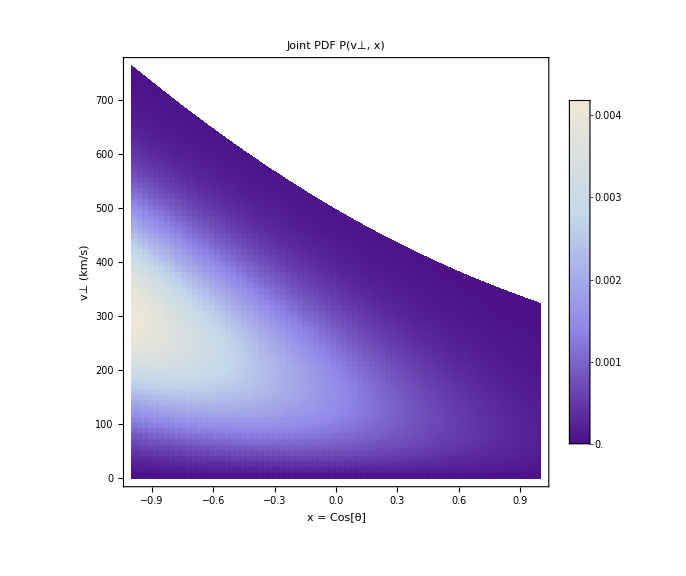

-Graphics-

Plotting the Contour Plot...

ContourPlot::cfun: Value of option ColorFunction -> Viridis is not a valid color function, or a gradient ColorData entity.

-Graphics-

-Graphics-

```mathematica
(*Parameters*)vL=220; (*km/s,Earth's speed relative to halo*)
v0=220; (*km/s,DM halo characteristic speed,often v0=vL for SHM*)
ve=544; (*km/s,Galactic escape velocity*)

(*Maximum perpendicular velocity due to escape velocity constraint*)
(*x_?NumericQ ensures this only evaluates for numerical x,useful for NIntegrate*)
vPerpMax[x_?NumericQ]:=Module[{valUnderSqrt,result},valUnderSqrt=ve^2-vL^2 (1-x^2);
If[valUnderSqrt<0,(*Should not happen if ve>vL*)0,result=-vL x+Sqrt[valUnderSqrt];
If[result<0,0,result] (*vPerp must be non-negative*)]];

(*Test vPerpMax for typical values*)
Print["vPerpMax[-1] (head-on, max possible v_perp if v_perp > 0) = ",vPerpMax[-1]]; (*Should be ve+vL*)
Print["vPerpMax[1] (receding, max possible v_perp if v_perp > 0) = ",vPerpMax[1]];   (*Should be ve-vL*)
Print["vPerpMax[0] (perpendicular incidence) = ",vPerpMax[0]]; (*Should be Sqrt[ve^2-vL^2]*)

(*Unnormalized PDF (proportional to v_perp*flux factor*Maxwellian)*)
(*vPerp_?NumericQ,x_?NumericQ ensures evaluation only for numerical inputs*)
unnormalizedPdf[vPerp_?NumericQ,x_?NumericQ]:=vPerp*Exp[-(vPerp+vL x)^2/v0^2];

(*Calculate the normalization constant C*)(*This NIntegrate can take a little time.We integrate vPerp from 0 up to vPerpMax[xVal].The outer integration for xVal is from-1 to 1.*)Print["Calculating normalization constant C... This may take a moment."];
normalizationConstantC=1/NIntegrate[unnormalizedPdf[vP,xVal],{xVal,-1,1},{vP,0,vPerpMax[xVal]},Method->"AdaptiveMonteCarlo",(*Or "LocalAdaptive",etc.if default struggles*)PrecisionGoal->6,AccuracyGoal->6,MaxRecursion->10];
Print["Normalization constant C = ",normalizationConstantC];

(*Normalized Joint PDF*)
jointPDF[vPerp_?NumericQ,x_?NumericQ]:=normalizationConstantC*unnormalizedPdf[vPerp,x];

(*Normalized Joint PDF*)
jointPDF[vPerp_?NumericQ,x_?NumericQ]:=normalizationConstantC*unnormalizedPdf[vPerp,x];

(*---Plotting the Joint PDF---*)

(*Determine a reasonable plot range for vPerp*)
maxPossibleVPerp=ve+vL; (*Absolute maximum v_perp occurs when x=-1*)

Print["Plotting the Density Plot..."];
densityPlot=DensityPlot[jointPDF[vP,xVal],{xVal,-1,1},{vP,0,maxPossibleVPerp},PlotRange->All,(*Let Mathematica scale the color intensity automatically*)ColorFunction->"Viridis",(*Or "SunsetColors","TemperatureMap",etc.*)PlotLegends->Automatic,FrameLabel->{"x = Cos[θ]","v⊥ (km/s)"},PlotLabel->"Joint PDF P(v⊥, x)",BaseStyle->{FontFamily->"Arial",FontSize->12},ImageSize->Large,(*RegionFunction is crucial to only plot where the PDF is defined*)RegionFunction->Function[{x,vp,fval},0<=vp<=vPerpMax[x]],Exclusions->None,(*Helps with potential discontinuities if any*)MaxRecursion->3,(*Increase for smoother plot,decrease for speed*)PlotPoints->75   (*Increase for smoother plot,decrease for speed*)]

(*Display the plot*)
Print[densityPlot]

(*You might also want a ContourPlot*)
Print["Plotting the Contour Plot..."];
contourPlot=ContourPlot[jointPDF[vP,xVal],{xVal,-1,1},{vP,0,maxPossibleVPerp},PlotRange->All,ColorFunction->"Viridis",Contours->15,(*Number of contour lines*)PlotLegends->Automatic,FrameLabel->{"x = Cos[θ]","v⊥ (km/s)"},PlotLabel->"Contour Plot of P(v⊥, x)",BaseStyle->{FontFamily->"Arial",FontSize->12},ImageSize->Large,RegionFunction->Function[{x,vp,fval},0<=vp<=vPerpMax[x]],Exclusions->None,MaxRecursion->3,PlotPoints->75]

(*Display the plot*)
Print[contourPlot]
```

DensityPlot::cfun: Value of option ColorFunction -> Viridis is not a valid color function, or a gradient ColorData entity.

Density Plot with Points (Epilog):

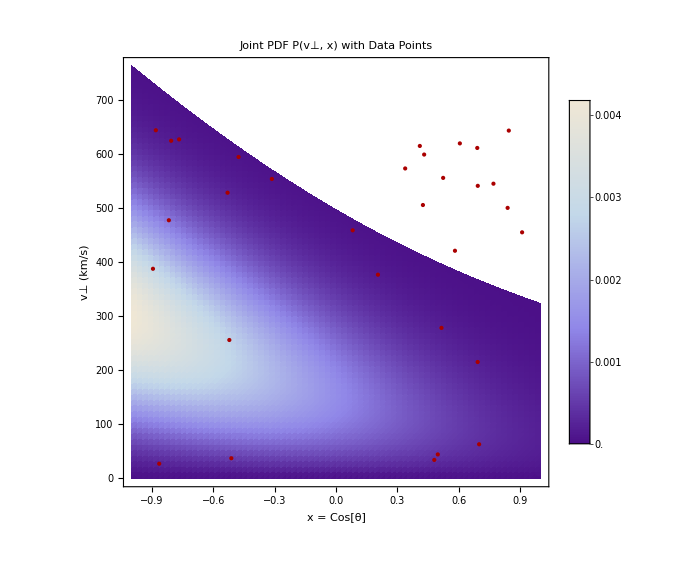

ContourPlot::cfun: Value of option ColorFunction -> Viridis is not a valid color function, or a gradient ColorData entity.

Contour Plot with Points (Epilog):

-Graphics-

```mathematica
(*Your data points*)dataPoints={{-0.8181208135,478.099},{0.4304156307,599.759},{0.6901330266,611.991},{-0.7679659202,627.845},{-0.8957978833,388.261},{0.5233126353,556.565},{0.4244257393,506.321},{-0.4772572288,595.277},{0.4092539863,615.697},{0.3376558503,574.013},{-0.5125686769,37.4368},{-0.8068992844,625.29},{0.8443918868,644.127},{0.204503569,377.336},{0.8386352048,501.017},{0.9094448043,455.761},{0.5150859474,278.817},{-0.5223405155,256.395},{-0.5309824637,529.124},{0.08096124055,459.445},{-0.8652510128,27.3333},{0.6920494457,215.637},{0.7693123658,545.824},{0.4971087488,44.5324},{0.6926818845,541.832},{0.4800155865,34.3478},{0.6049877447,620.421},{0.5811038631,421.639},{-0.3143245116,554.585},{0.6992756731,63.3276},{-0.8817642362,644.776}};

(*---Assuming the previous code for PDF calculation and plotting is already run---*)
(*If not,you need to run the parameter definitions,vPerpMax,unnormalizedPdf,*)
(*normalizationConstantC,jointPDF,and the densityPlot/contourPlot definitions.*)

(*Method 1:Using Epilog (simpler for just adding points)*)
densityPlotWithPointsEpilog=DensityPlot[jointPDF[vP,xVal],{xVal,-1,1},{vP,0,maxPossibleVPerp},PlotRange->All,ColorFunction->"Viridis",PlotLegends->Automatic,FrameLabel->{"x = Cos[θ]","v⊥ (km/s)"},PlotLabel->"Joint PDF P(v⊥, x) with Data Points",BaseStyle->{FontFamily->"Arial",FontSize->12},ImageSize->Large,RegionFunction->Function[{x,vp,fval},0<=vp<=vPerpMax[x]],Exclusions->None,MaxRecursion->3,PlotPoints->75,Epilog->{PointSize[Large],(*Adjust point size*)Darker[Red],(*Adjust point color*)Point[dataPoints]}];

Print["Density Plot with Points (Epilog):"];
Print[densityPlotWithPointsEpilog];

contourPlotWithPointsEpilog=ContourPlot[jointPDF[vP,xVal],{xVal,-1,1},{vP,0,maxPossibleVPerp},PlotRange->All,ColorFunction->"Viridis",Contours->15,PlotLegends->Automatic,FrameLabel->{"x = Cos[θ]","v⊥ (km/s)"},PlotLabel->"Contour Plot of P(v⊥, x) with Data Points",BaseStyle->{FontFamily->"Arial",FontSize->12},ImageSize->Large,RegionFunction->Function[{x,vp,fval},0<=vp<=vPerpMax[x]],Exclusions->None,MaxRecursion->3,PlotPoints->75,Epilog->{PointSize[Large],Darker[Red],Point[dataPoints]}];

Print["Contour Plot with Points (Epilog):"];
Print[contourPlotWithPointsEpilog];
```

```mathematica
(*---Interactive Input for PDF Value---*)
Print["\n--- Get PDF Value at a Specific Point ---"];
Manipulate[DynamicModule[{pdfResult="Enter values and click 'Get PDF'"},Column[{Row[{Control[{{inputCosTheta,0.0,"Cos[θ] (x):"},-1,1,Appearance->"Labeled"}],Spacer[20],Control[{{inputVPerp,300.0,"v⊥ (km/s):"},0,ve+vL,Appearance->"Labeled"}]}],Button["Get PDF Value",pdfResult=jointPDFValue[inputVPerp,inputCosTheta];
If[pdfResult===$Failed,pdfResult="Invalid input.",pdfResult=Row[{"P(",inputVPerp,", ",inputCosTheta,") ≈ ",NumberForm[pdfResult,{Infinity,6}]}]]],Dynamic[Style[pdfResult,If[pdfResult==="Invalid input."||StringContainsQ[ToString[pdfResult],"Error"],Red,Black],12]]},Alignment->Center]],SaveDefinitions->True (*Important for Manipulate to remember function definitions*)]
```

--- Get PDF Value at a Specific Point ---